```mathematica
f[a_,b_,th_]=r[th]/.DSolve[{r'[th]==b r[th],r[0]==a},r[th],th][[1]];
```

```mathematica
gra1=ParametricPlot[{f[0.1,0.1,th] Cos[th],f[0.1,0.1,th]  Sin[th]},{th,0,8 Pi}]
gra2 = ParametricPlot[{f[0.01,0.01,th] Cos[th],f[0.01,0.01,th]  Sin[th]},{th,0,8 Pi}]
```

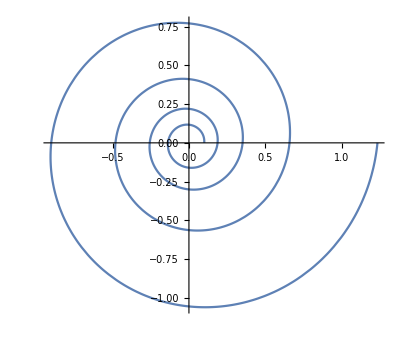
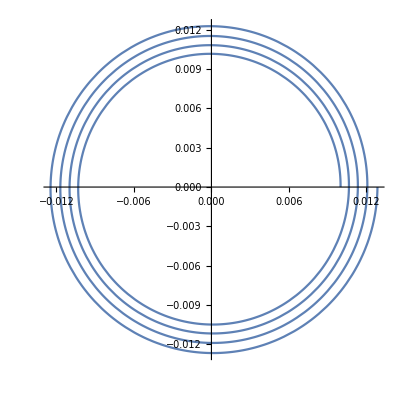

```mathematica
{gra1,gra2}
```

```mathematica
thetha[i_] := Pi/180 + 2 (Pi/5)  i;
thetha[0] := Pi/180;
x[i_] := (y[i-1]-x[i-1] Tan[thetha[i-1]+(Pi /2)] )/(Tan[thetha[i]] - Tan[thetha[i-1+ (Pi/2)]]);
x[0] := 0.01;
y[i_] := x[i] Tan[thetha[i]];
y[0] :=x[0]*Tan[thetha[0]];
```

```mathematica
g= Table[thetha[i]; a=x[i]; b=y[i]; {a,b}, {i,0,5}] (*Non funziona bene*)
```

{{0.01,0.000174551},{0.104069,0.340395},{-0.461213,0.322945},{-0.245979,-0.185358},{0.219732,-0.638148},{0.805625,0.0140622}}

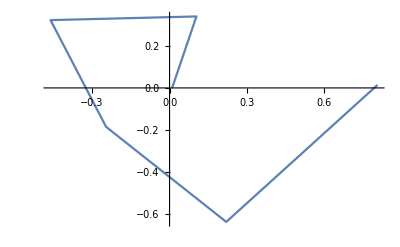

```mathematica
ListPlot[g,Joined->True]
```

```mathematica
M={{-m1^2-k,k},{k,-k-m2^2}};
eig=Eigenvalues[M];
```

```mathematica
TH={th1[t],th2[t]};

m2=m;
m1=m;

sol1=Solve[M.TH==eig[[1]] TH,TH]/.{1/Sqrt[k^2]->1/k};
sol2=Solve[M.TH==eig[[2]] TH,TH]/.{1/Sqrt[k^2]->1/k};

eqs={th1''[t]==-m1^2 th1[t]-k th1[t]+k th2[t],
      th2''[t]==-m2^2 th2[t]+k th1[t]-k th2[t],
      th1'[0]==0,
      th2'[0]==0,
      th1[0]==th1bar,
      th2[0]==th2bar
};

sol=DSolve[eqs,TH,t];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
somma[t_]=(th1[t]+th2[t])/.sol/.{th2bar->th1bar}



differenzia[t_]=(th1[t]-th2[t])/.sol/.{th2bar->-th1bar}

valori={th1bar->0.5,th2bar->0.5,m->1,k->1}
gra2=Plot[{somma[t][[1]]/.valori,differenzia[t][[1]]/.valori},{t,0,10}]
```

{1/2 ⅇ^(-ⅈ m t-√(-2 k-m^2) t) (2 ⅇ^(√(-2 k-m^2) t) th1bar+2 ⅇ^(2 ⅈ m t+√(-2 k-m^2) t) th1bar)}

{-1/4 ⅇ^(-ⅈ m t-√(-2 k-m^2) t) (-2 ⅇ^(ⅈ m t) th1bar-2 ⅇ^(ⅈ m t+2 √(-2 k-m^2) t) th1bar)+1/4 ⅇ^(-ⅈ m t-√(-2 k-m^2) t) (2 ⅇ^(ⅈ m t) th1bar+2 ⅇ^(ⅈ m t+2 √(-2 k-m^2) t) th1bar)}

{th1bar→0.5,th2bar→0.5,m→1,k→1}

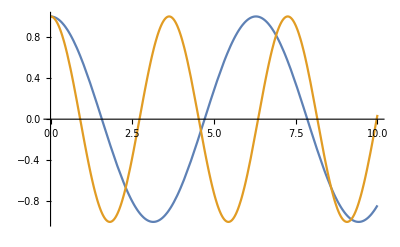
```mathematica
-Graphics-
valori2={th2bar->0,m->1}

sol3[t_,k_,th1bar_]=th1[t]/.sol/.valori2;
grafico[k_,th1bar_]:=Plot[sol3[t,k,th1bar],{t,0,100}]
```

-Graphics-

{th2bar→0,m→1}

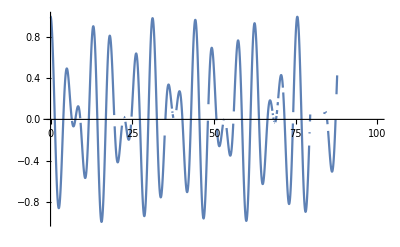
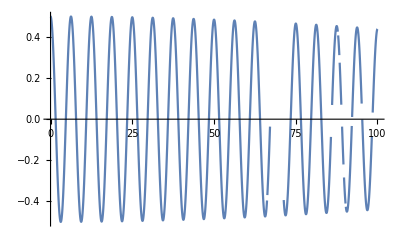
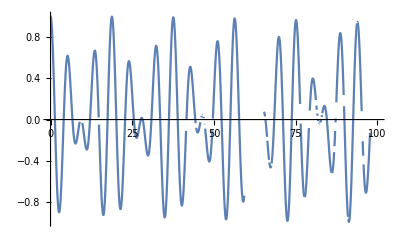

```mathematica
{grafico[0.5,1],grafico[0.01,0.5], grafico[0.4,1]}
```

```mathematica
??Manipulate
```

Manipulate[expr,{u,u_min,u_max}] generates a version of expr with controls added to allow interactive manipulation of the value of u. 
Manipulate[expr,{u,u_min,u_max,du}] allows the value of u to vary between u_min and u_max in steps du. 
Manipulate[expr,{{u,u_init},u_min,u_max,…}] takes the initial value of u to be u_init. 
Manipulate[expr,{{u,u_init,u_lbl},…}] labels the controls for u with u_lbl. 
Manipulate[expr,{u,{u_1,u_2,…}}] allows u to take on discrete values u_1,u_2,…. 
Manipulate[expr,{u,…},{v,…},…] provides controls to manipulate each of the u,v,…. 
Manipulate[expr,c_u→{u,…},c_v→{v,…},…] links the controls to the specified controllers on an external device.

Attributes[Manipulate]={HoldAll,Protected,ReadProtected}
 
Options[Manipulate]={Alignment→Automatic,AppearanceElements→Automatic,AutoAction→False,AutorunSequencing→Automatic,BaselinePosition→Automatic,BaseStyle→{},Bookmarks→{},ContentSize→Automatic,ContinuousAction→Automatic,ControlAlignment→Automatic,ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,ControlPlacement→Automatic,ControlType→Automatic,DefaultBaseStyle→Manipulate,DefaultLabelStyle→ManipulateLabel,Deinitialization:>None,Deployed→False,Evaluator→Automatic,Frame→False,FrameLabel→None,FrameMargins→Automatic,ImageMargins→0,Initialization:>None,InterpolationOrder→Automatic,LabelStyle→{},LocalizeVariables→True,Method→{},Paneled→True,PreserveImageOptions→True,RotateLabel→False,SaveDefinitions→False,ShrinkingDelay→0,SynchronousInitialization→True,SynchronousUpdating→Automatic,TouchscreenAutoZoom→False,TouchscreenControlPlacement→Automatic,TrackedSymbols→Full,UndoTrackedVariables:>None,UnsavedVariables:>None,UntrackedVariables:>None}